## Finding the resonant frequency

```mathematica
EquationForced = {
(J1 Sin[2 θ[t]] (D[ϕ[t],t])^2)/2-J1 D[θ[t],{t, 2}]-J3 Sin[θ[t]] D[ϕ[t],t] D[ψ[t],t]-(J3 Sin[2 θ[t]] (D[ϕ[t],t])^2)/2+g h m Sin[θ[t]]+(h^2 m Sin[2 θ[t]] (D[ϕ[t],t])^2)/2-h^2 m D[θ[t],{t, 2}]+h m w^2 x0 Sin[t w] Sin[ϕ[t]] Cos[θ[t]]==0,
-J1 Sin[θ[t]]^2 D[ϕ[t],{t, 2}]-J1 Sin[2 θ[t]] D[ϕ[t],t] D[θ[t],t]+J3 Sin[θ[t]]^2 D[ϕ[t],{t, 2}]+J3 Sin[θ[t]] D[ψ[t],t] D[θ[t],t]+J3 Sin[2 θ[t]] D[ϕ[t],t] D[θ[t],t]-J3 Cos[θ[t]] D[ψ[t],{t, 2}]-J3 D[ϕ[t],{t, 2}]-h^2 m Sin[θ[t]]^2 D[ϕ[t],{t, 2}]-h^2 m Sin[2 θ[t]] D[ϕ[t],t] D[θ[t],t]+h m w^2 x0 Sin[t w] Sin[θ[t]] Cos[ϕ[t]]==0,
J3 (Sin[θ[t]] D[ϕ[t],t] D[θ[t],t]-Cos[θ[t]] D[ϕ[t],{t, 2}]-D[ψ[t],{t, 2}])==0,
θ[0] == Pi/6,
ϕ[0] == 0, 
ψ[0] == 0, 
θ'[0] == 0,
ϕ'[0] ==0 , 
ψ'[0] ==  2Pi * hz};
```

```mathematica
Listω = Range[2*Pi*0.4,2*Pi*0.6, 0.01];
```

```mathematica
Subscript[Listθ, max, 100] = Table[NMaximize[(θ[t]/. (Flatten@NDSolve[EquationForced /. {w ->k, hz -> 100}, {θ[t], ϕ[t], ψ[t]}, {t, 0., 300.}])), {t, 0., 100.}, Method->"DifferentialEvolution"][[1]],
{k, 2*Pi*0.4,2*Pi*0.6, 0.01}];
```

```mathematica
Subscript[Coupleωθ, max, 100]= Transpose[{Listω, Subscript[Listθ, max]}]
```

{{3.14159,0.907322},{3.15159,0.925418},{3.16159,0.945588},{3.17159,0.966552},{3.18159,0.988879},{3.19159,1.00836},{3.20159,1.03898},{3.21159,1.07505},{3.22159,1.1158},{3.23159,1.16884},{3.24159,1.23004},{3.25159,1.30923},{3.26159,1.43188},{3.27159,1.81291},{3.28159,2.84707},{3.29159,2.64419},{3.30159,2.47639},{3.31159,2.3313},{3.32159,2.20316},{3.33159,2.08274},{3.34159,1.9705},{3.35159,1.85947},{3.36159,1.76335},{3.37159,1.66433},{3.38159,1.57036},{3.39159,1.47164},{3.40159,1.38742},{3.41159,1.29485},{3.42159,1.21448},{3.43159,1.12308},{3.44159,1.04635},{3.45159,0.961644},{3.46159,0.886363},{3.47159,0.81005},{3.48159,0.732245},{3.49159,0.662919},{3.50159,0.596579},{3.51159,0.567734},{3.52159,0.567732},{3.53159,0.567731},{3.54159,0.567729},{3.55159,0.567728},{3.56159,0.567726},{3.57159,0.567725},{3.58159,0.567723},{3.59159,0.567722},{3.60159,0.56772},{3.61159,0.567719},{3.62159,0.567717},{3.63159,0.567715},{3.64159,0.565985},{3.65159,0.567712},{3.66159,0.565101},{3.67159,0.567709},{3.68159,0.567707},{3.69159,0.567705},{3.70159,0.567704},{3.71159,0.567702},{3.72159,0.5677},{3.73159,0.567699},{3.74159,0.567697},{3.75159,0.567695},{3.76159,0.567694}}

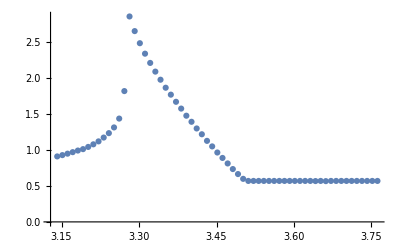

```mathematica
ListPlot[Subscript[Coupleωθ, max]]
```

```mathematica
Subscript[Listθ, max, 105] = Table[NMaximize[(θ[t]/. (Flatten@NDSolve[EquationForced /. {w ->k, hz -> 105}, {θ[t], ϕ[t], ψ[t]}, {t, 0., 300.}])), {t, 0., 100.}, Method->"DifferentialEvolution"][[1]],
{k, 2*Pi*0.4,2*Pi*0.6, 0.01}];
```

InterpolatingFunction::dmval: Input value {693.134} lies outside the range of data in the interpolating function. Extrapolation will be used.

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

NDSolve::ndsz: At t == 202.771, step size is effectively zero; singularity or stiff system suspected.

```mathematica
Subscript[Coupleωθ, max, 105]= Transpose[{Listω, Subscript[Listθ, max, 105]}]
```

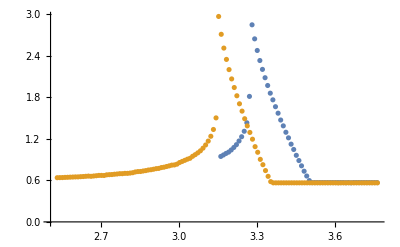

```mathematica
ListPlot[{Subscript[Coupleωθ, max][[3;;]], Subscript[Coupleωθ, max, 105][[3;;]]}, PlotRange->All]
```

```mathematica
Subscript[Listθ, max, 105] = Table[NMaximize[(θ[t]/. (Flatten@NDSolve[EquationForced /. {w ->k, hz -> 101}, {θ[t], ϕ[t], ψ[t]}, {t, 0., 300.}])), {t, 0., 100.}, Method->"DifferentialEvolution"][[1]],
{k, 2*Pi*0.5,2*Pi*0.6, 0.01}];
```